### Case estimates

```mathematica
days = Table[17+i,{i,8,14}];
```

### We obtained the number of confirmed infectious cases in China except the province of Hubei from January 25th to January 31st from the openly accessible database of Johns Hopkins University (https://docs.google.com/spreadsheets/d/1yZv9w9zRKwrGTaR-YzmAqMefw4wMlaXocejdxZaTs6w). We also added the cumulative number of infectious cases in Hubei until before the quarantine was applied on January 24th, because they can also contribute to later incidences.

```mathematica
conf= List[591+549,927+549,1314+549,1695+549,2416+549,3092+549,4005+549];
```

### Taking the significant underreporting into account, we calculated a maximum - likelihood estimate for the cumulative infectious cases with EpiRisk (epirisk.net), considering how many infectious cases in China produce the known number of imported cases from January 25th to January 31st. We supposed that the number of imported cases from China are not underreported. The lists below contain the left endpoints, the means and the right endpoints of the ML-intervals, respectively.

```mathematica
under = List[19450,22750,32100,36600,46550,59200,66000];
```

```mathematica
middle = List[19150,22475,31850,36300,46275,58950,65750];
```

```mathematica
over = List[18850,22200,31600,36000,46000,58700,65500];
```

```mathematica
ratiounder = Table[conf[[i]]/under[[i]],{i,1,7}];
```

```mathematica
ratiomiddle= Table[conf[[i]]/middle[[i]],{i,1,7}];
```

```mathematica
ratioover = Table[conf[[i]]/over[[i]],{i,1,7}];
```

```mathematica
dotsunder = Table[{days[[i]],ratiounder[[i]]},{i,1,7}];
```

```mathematica
dotsmiddle= Table[{days[[i]],ratiomiddle[[i]]},{i,1,7}];
```

```mathematica
dotsover = Table[{days[[i]],ratioover[[i]]},{i,1,7}];
```

```mathematica
meanunder=Mean[ratiounder];
```

```mathematica
meanmiddle=Mean[ratiomiddle];
```

```mathematica
meanover=Mean[ratioover];
```

```mathematica
g1 =ListPlot[dotsover,PlotRange->{0.046,0.076},BaseStyle->{20,Bold}];
```

```mathematica
g2 =ListPlot[dotsunder,PlotRange->{0.045,0.075},BaseStyle->{20,Bold}];
```

```mathematica
g3 =ListPlot[dotsmiddle,PlotStyle->Black,PlotRange->{0.045,0.075},BaseStyle->{20, Bold}];
```

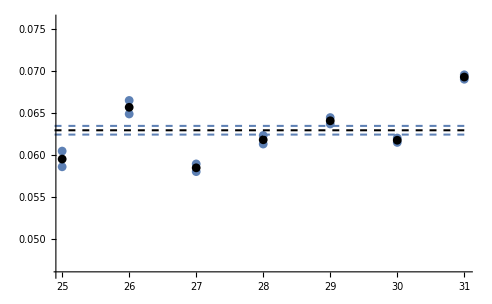

```mathematica
Show[g1,g2,g3,Plot[meanover,{x,24,31},PlotStyle->{Dashed,Thickness[0.003]}],Plot[meanunder,{x,24,31},PlotStyle->{Dashed,Thickness[0.003]}],Plot[meanmiddle,{x,24,31},PlotStyle->{Dashed, Black,Thickness[0.003]}]]
```

### With this method we found a relatively stable ascertainment rate during that week, around 6.3%. Next we use this rate to estimate real case numbers from confirmed case numbers outside Hubei.

```mathematica
data=ConfCases=N[{{0,316},{0.5,367},{1,591},{1.5,638},{1+22/24,927},{2+11/24,1004},{2+23/24,1314},{3+9/24,1402},{3+19/24,1440},{3+20.5/24,1695},{4+13/24,1896},{4.75,1940},{4+23/24,2416},{5+13.5/24,2516},{5+21/24,3092},{6+11/24,3221}}]
```

{{0.,316.},{0.5,367.},{1.,591.},{1.5,638.},{1.91667,927.},{2.45833,1004.},{2.95833,1314.},{3.375,1402.},{3.79167,1440.},{3.85417,1695.},{4.54167,1896.},{4.75,1940.},{4.95833,2416.},{5.5625,2516.},{5.875,3092.},{6.45833,3221.}}

```mathematica
For[i=0,i<Length[ConfCases],data[[i,2]]=ConfCases[[i,2]]*14.9468,i++];
data
```

{{0.,4723.19},{0.5,5485.48},{1.,8833.56},{1.5,9536.06},{1.91667,13855.7},{2.45833,15006.6},{2.95833,19640.1},{3.375,20955.4},{3.79167,21523.4},{3.85417,25334.8},{4.54167,28339.1},{4.75,28996.8},{4.95833,36111.5},{5.5625,37606.1},{5.875,46215.5},{6.45833,48143.6}}

### We parametrically solve the SEIR model with respect to initial values.

```mathematica
Pop=1437000000-58160000; (*China-Hubei*)
IncubationPeriod=5.1; 
R0=2.6; (*2.1, 2.6, 3.1*)
InfectiousPeriod=3.3; (*1.7, 3.3, 5.6*)
sol=ParametricNDSolve[{s'[t]==-(R0/(Pop * InfectiousPeriod))*s[t]*(i1[t]+i2[t]+i3[t]),e1'[t]==(R0/(Pop * InfectiousPeriod))*s[t]*(i1[t]+i2[t]+i3[t])-(2/IncubationPeriod)*e1[t],e2'[t]== (2/IncubationPeriod)*e1[t]-(2/IncubationPeriod)*e2[t],i1'[t]== (2/IncubationPeriod)*e2[t]-(3/InfectiousPeriod)*i1[t],i2'[t]== (3/InfectiousPeriod)*i1[t]-(3/InfectiousPeriod)*i2[t],i3'[t]==(3/InfectiousPeriod)*i2[t]-(3/InfectiousPeriod)*i3[t],R'[t]== (3/InfectiousPeriod)*i3[t],Cu'[t]==(2/IncubationPeriod)*e2[t],s[0]==Pop-(Ex1+Ex2+ix1+ix2+ix3),e1[0]==Ex1,e2[0]==Ex2,i1[0]==ix1,i2[0]==ix2,i3[0]==ix3,Cu[0]==ix1+ix2+ix3,R[0]==0},{s,e1,e2,i1,i2,i3,Cu,R},{t,0,10},{Ex1,Ex2,ix1,ix2,ix3}];
```

### We find the best fit to data.

```mathematica
para=FindMinimum[{Sum[(Cu[Ex1,Ex2,ix1,ix2,ix3][data[[i,1]]]-data[[i,2]])^2/.sol,{i,1,Length[data]}],Ex1>Ex2>ix1>ix2>ix3≥0},{{Ex1,10500},{Ex2,10500},{ix1,1500},{ix2,1000},{ix3,1000}}]//Quiet
```

{5.08349×10^7,{Ex1→27503.6,Ex2→4537.7,ix1→4537.7,ix2→1.80757,ix3→1.23645}}

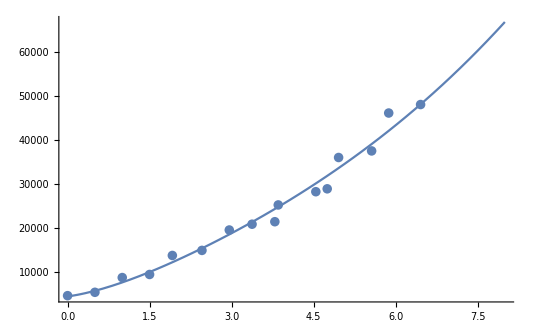

```mathematica
Show[Plot[Evaluate[{Cu[Ex1,Ex2,ix1,ix2,ix3][t]}/.sol/.Last[para]],{t, 0,8}],ListPlot[data],PlotRange->All]
```

### Define the control term

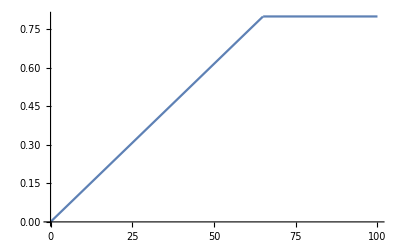

```mathematica
T=50; (*20--50*)
umax=0.8;
u[t_]=Min[(1-1/R0)t/T,umax];
Plot[u[t],{t,0,100}]
```

### Solve the transmission model with control

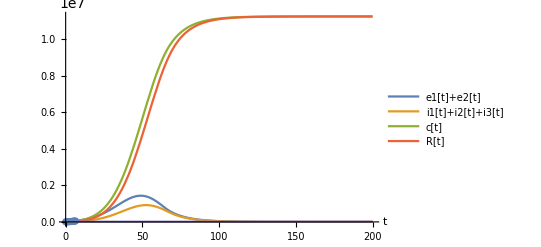

```mathematica
{Ex1,Ex2,ix1,ix2,ix3}={Ex1,Ex2,ix1,ix2,ix3}/.Last[para];Show[{Plot[{Evaluate[{e1[t]+e2[t],i1[t]+i2[t]+i3[t],c[t],R[t],9000}/.First[NDSolve[{s'[t]==-(1-u[t])(R0/(Pop * InfectiousPeriod))*s[t]*(i1[t]+i2[t]+i3[t]),e1'[t]==(1-u[t])(R0/(Pop * InfectiousPeriod))*s[t]*(i1[t]+i2[t]+i3[t])-(2/IncubationPeriod)*e1[t],e2'[t]== (2/IncubationPeriod)*e1[t]-(2/IncubationPeriod)*e2[t],i1'[t]== (2/IncubationPeriod)*e2[t]-(3/InfectiousPeriod)*i1[t],i2'[t]== (3/InfectiousPeriod)*i1[t]-(3/InfectiousPeriod)*i2[t],i3'[t]==(3/InfectiousPeriod)*i2[t]-(3/InfectiousPeriod)*i3[t],R'[t]== (3/InfectiousPeriod)*i3[t],c'[t]== (2/IncubationPeriod)*e2[t],s[0]==Pop-Ex1-Ex2-ix1-ix2-ix3,e1[0]==Ex1,e2[0]==Ex2,i1[0]==ix1,i2[0]==ix2,i3[0]==ix3,c[0]==ix1+ix2+ix3,R[0]==0},{s,e1,e2,i1,i2,i3,c,R},{t,0,200}]]]},{t,0,200},AxesLabel->Automatic, 
PlotLegends->{"e1[t]+e2[t]","i1[t]+i2[t]+i3[t]","c[t]","R[t]"},PlotRange->{{0,200},Full}],ListPlot[data]}]
```

Input to final size integrator in python

incubation period 5.1

R0=2.1
infectious period 1.7
i1(0)=4619
i2(0)=18
i3(0)=14
e1(0)=24163
e2(0)=4619

R0=2.6
infectious period 3.3
i1(0)=4538
i2(0)=2
i3(0)=1
e1(0)=27504
e2(0)=4538

R0=3.1
infectious period 5.6
i1(0)=4088
i2(0)=90
i3(0)=0
e1(0)=32677
e2(0)=4088